```mathematica
X={(*100,388,500,*)1000,5000,10000,20000,50000};
y={(*191.8,388.4,455.7,*)536.5,998.9,1516,2526,5743}*12;
```

```mathematica
Clear@f
f[x_]=FindFormula[{X,y}ᵀ,x]
```

5332.02+1.26959 x

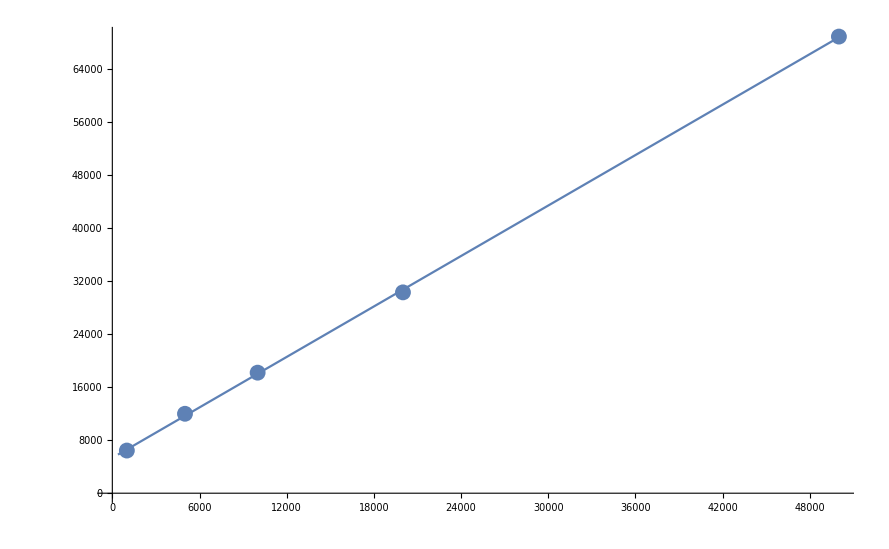

```mathematica
Show[ListPlot[{X,y}ᵀ],Plot[f[x],{x,388,50000}]]
```